# Wolfram/AdvancedSamplePaclet

A sample paclet used to demonstrate more complex CI/CD workflows at the 2022 Wolfram Technology Conference

## Paclet Manifest

"Documentation"

"English"

"Guides"

"SampleGuide.nb"DocumentationEnglishGuidesSampleGuide.nb

"ReferencePages"

"Symbols"

"AddOne.nb"DocumentationEnglishReferencePagesSymbolsAddOne.nb

"AddTwo.nb"DocumentationEnglishReferencePagesSymbolsAddTwo.nb

"Tutorials"

"Arithmetic.nb"DocumentationEnglishTutorialsArithmetic.nb

"Kernel"

"AddOne.wl"KernelAddOne.wl

"AddTwo.wl"KernelAddTwo.wl

"AdvancedSamplePaclet.wl"KernelAdvancedSamplePaclet.wl

"Libraries.wl"KernelLibraries.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

"Scripts"

"BuildMX.wls"ScriptsBuildMX.wls

"Compile.wls"ScriptsCompile.wls

"SetBuildDate.wls"ScriptsSetBuildDate.wls

"Source"

"AddOne.c"SourceAddOne.c

"AddTwo.c"SourceAddTwo.c

"Library.c"SourceLibrary.c

"Tests"

"AddOne.wlt"TestsAddOne.wlt

"AddTwo.wlt"TestsAddTwo.wlt

## Web Content

### Headline Image

```mathematica
url="https://www.wolfram.com/events/technology-conference/2022/img/WTC-2022-date.svg";
svg=ResourceFunction["SVGImport"][url];
Show[svg,PlotRange->{{-25,385},{0,360}},ImageSize->Automatic]
```

-Graphics-

### Basic Description

This is a sample paclet used for a PacletCICD demo at the 2022 Wolfram Technology Conference. This paclet is meant to demonstrate more advanced CI/CD workflows that involves:

- standard paclet checks

- multi-platform compilation

- automated tests

- MX builds

- separate workflows for pull requests and releases

The full source for this paclet can be found on GitHub here.

### Details

Additional information about the paclet.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["Wolfram`AdvancedSamplePaclet`"];
```

### Basic Examples

Here is a basic example:

```mathematica
AddOne[1]
```

2

Here's another example for a different function:

```mathematica
AddTwo[1]
```

3

Create a very interesting Plot:

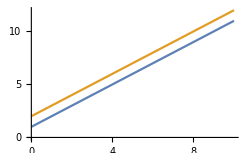

```mathematica
Plot[{AddOne[x],AddTwo[x]},{x,0,10}]
```

### Scope

Add to symbols:

```mathematica
AddOne[x]
```

1+x

```mathematica
AddTwo[x]
```

2+x

Create new functions that no one has ever thought of before:

```mathematica
addThree=AddOne@*AddTwo
```

AddOne@*AddTwo

```mathematica
addThree[1]
```

4

```mathematica
naturalNumber[n_]:=Nest[AddOne,0,n];
```

Simply incredible:

```mathematica
naturalNumber[5]
```

5

### Applications

Reinvent arithmetic:

```mathematica
plus[x_,y_]:=Nest[AddOne,x,y];
```

```mathematica
plus[3,4]
```

7

```mathematica
times[x_,y_]:=Nest[OperatorApplied[plus][x],0,y];
```

```mathematica
times[3,4]
```

12

Weird numbers like negative integers and reals are too hard and can therefore be assumed to not exist.

### Properties and Relations

AddTwo can be implemented using only AddOne:

```mathematica
AddTwo[x]
```

2+x

```mathematica
addTwo=AddOne@*AddOne;
```

```mathematica
addTwo[x]
```

2+x

AddOne is the best function:

```mathematica
[Row[{AddOne," is simply the best"}]]
```

-Graphics-

## Source & Additional Information

### Creator

Richard Hennigan (Wolfram Research)

### Source Control Repository

https://github.com/rhennigan/AdvancedSamplePaclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Wolfram Technology Conference

Sample Paclet

Compiled Code

CI/CD

Dev Ops

GitHub

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Wolfram/PacletCICD

### Original Source References and Attributions

Source, reference or citation

### Links

Wolfram Technology Conference 2022

PacletCICD | Wolfram Language Paclet Repository

PacletCICD | GitHub

AdvancedSamplePaclet | GitHub

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.